## Leading order contribution to qq̄→(χ̃)_i^0(χ̃)_j^0

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of three packages found in the “include” folder.

```mathematica
description = "Leading order cross section of neutralino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< TreeLevel`
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

## Generate Feynman diagrams and amplitudes

Some text

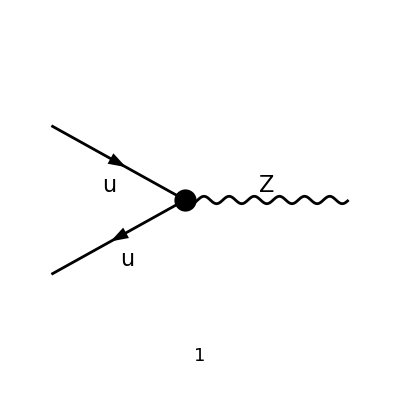

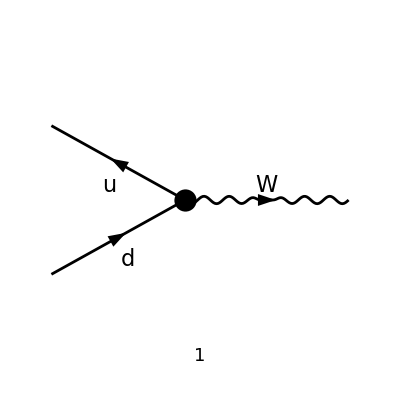

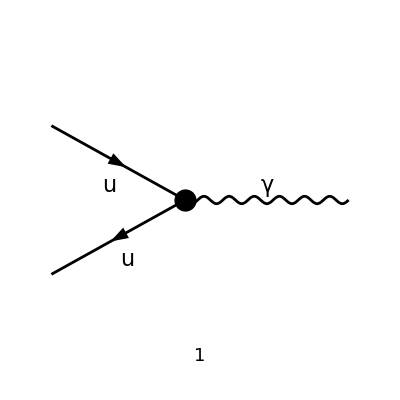

```mathematica
ZDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 1], 
	{F[3, {1}], -F[3, {1}]} -> {V[2]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}
];
WDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 1], 
	{-F[3, {1}], F[4, {1}]} -> {V[3]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}
];
ADiagrams = InsertFields[
	CreateTopologies[0, 2 -> 1], 
	{F[3, {1}], -F[3, {1}]} -> {V[1]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}
];
Paint[ZDiagrams, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];
Paint[WDiagrams, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];
Paint[ADiagrams, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];
```

```mathematica
MZ[0] = FCFAConvert[
	CreateFeynAmp[ZDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;
MW[0] = FCFAConvert[
	CreateFeynAmp[WDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta, SMP["m_d"] -> 0} /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;
MA[0] = FCFAConvert[
	CreateFeynAmp[ADiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta, SMP["m_d"] -> 0} /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;
```

```mathematica
MZ[1] = MZ[0] /. ZSimplifyRules;
MW[1] = MW[0] /. WSimplifyRules;
MA[1] = MA[0] /. SMP["sin_W"] -> 3/2 Qe SMP["sin_W"];
{MZ[2], MW[2], MA[2]} = DiracSimplify /@ {MZ[1], MW[1], MA[1]}
```

{g_W (-C_qqZ^R) δ_Col1Col2 (φ(-k_j)).γ^μ.(γ̄)^6.(φ(k_i))-g_W C_qqZ^L δ_Col1Col2 (φ(-k_j)).γ^μ.(γ̄)^7.(φ(k_i)),g_W δ_Col1Col2 (-C_(q q' W)^L) (φ(-k_i)).γ^μ.(γ̄)^7.(φ(k_j)),-Qe g_W δ_Col1Col2 (sin(θ_W)) (φ(-k_j)).γ^μ.(φ(k_i))}

## Set scalar products

```mathematica
SPD[ki, ki] = 0;
SPD[kj, kj] = 0;
SPD[ki, kj] = s/2;
SPD[ki, q] = s/2;
SPD[kj, q] = s/2;
SPD[q, q] = s;
```

## Evaluate square amplitudes

### Z part

Square the amplitude and simplify sum over fermion chains and polarisations of emitted gluon. Also disregard remaining Dirac traces with 4 γ-matrices and γ5.

```mathematica
ZTensor[0] = (MZ[2] ConjugateAmplitude[MZ[2]/.μ->ν]) // FermionSpinSum // DiracSimplify;
ZTensor[1] = SelectFree2[ZTensor[0], DiracTrace];
```

Now we can make the result more presentable by calculating the colour factor and extracting a common prefactor.

```mathematica
CommonPrefactor = SMP["g_W"]^2 SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]^2;
ZTensor[2] = CommonPrefactor (ZTensor[1]/CommonPrefactor // Collect2[#, Pair[__], Factoring->Simplify]&)
```

g_W^2 δ_Col1Col2^2 (-s g^μν ((C_qqZ^L)^2+(C_qqZ^R)^2)+2 k_i^ν k_j^μ ((C_qqZ^L)^2+(C_qqZ^R)^2)+2 k_i^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
ZTensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] ZTensor[2] // DoPolarizationSums[#, q]&;
ZTensorContracted[1] = ZTensorContracted[0] // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

(D-2) s g_W^2 δ_Col1Col2^2 ((C_qqZ^L)^2+(C_qqZ^R)^2)

### W part

Square the amplitude and simplify sum over fermion chains and polarisations of emitted gluon. Also disregard remaining Dirac traces with 4 γ-matrices and γ5.

```mathematica
WTensor[0] = (MW[2] ConjugateAmplitude[MW[2]/.μ->ν]) // FermionSpinSum // DiracSimplify;
WTensor[1] = SelectFree2[WTensor[0], DiracTrace];
```

Now we can make the result more presentable by calculating the colour factor and extracting a common prefactor.

```mathematica
CommonPrefactor = SMP["g_W"]^2 SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]^2;
WTensor[2] = CommonPrefactor (WTensor[1]/CommonPrefactor // Collect2[#, Pair[__], Factoring->Simplify]&)
```

g_W^2 δ_Col1Col2^2 (-s g^μν C_(q q' W)^L Conjugate[(C_(q q' W)^L)]+2 k_i^ν k_j^μ C_(q q' W)^L Conjugate[(C_(q q' W)^L)]+2 k_i^μ k_j^ν C_(q q' W)^L Conjugate[(C_(q q' W)^L)])

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
WTensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] WTensor[2] // DoPolarizationSums[#, q]&;
WTensorContracted[1] = WTensorContracted[0] // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

(D-2) s g_W^2 δ_Col1Col2^2 C_(q q' W)^L Conjugate[(C_(q q' W)^L)]

### A part

Square the amplitude and simplify sum over fermion chains and polarisations of emitted gluon. Also disregard remaining Dirac traces with 4 γ-matrices and γ5.

```mathematica
ATensor[0] = (MA[2] ConjugateAmplitude[MA[2]/.μ->ν]) // FermionSpinSum // DiracSimplify;
ATensor[1] = SelectFree2[ATensor[0], DiracTrace];
```

Now we can make the result more presentable by calculating the colour factor and extracting a common prefactor.

```mathematica
CommonPrefactor = SMP["g_W"]^2 SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]^2;
ATensor[2] = CommonPrefactor (ATensor[1]/CommonPrefactor // Collect2[#, Pair[__], Factoring->Simplify]&)
```

g_W^2 δ_Col1Col2^2 (-2 Qe^2 s g^μν (sin(θ_W))^2+4 Qe^2 k_i^ν k_j^μ (sin(θ_W))^2+4 Qe^2 k_i^μ k_j^ν (sin(θ_W))^2)

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
ATensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] ATensor[2] // DoPolarizationSums[#, q]&;
ATensorContracted[1] = ATensorContracted[0] // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

2 (D-2) Qe^2 s g_W^2 δ_Col1Col2^2 (sin(θ_W))^2

### AZ part

Square the amplitude and simplify sum over fermion chains and polarisations of emitted gluon. Also disregard remaining Dirac traces with 4 γ-matrices and γ5.

```mathematica
AZTensor[0] = (MA[2] ConjugateAmplitude[MZ[2]/.μ->ν]) // FermionSpinSum // DiracSimplify;
AZTensor[1] = SelectFree2[AZTensor[0], DiracTrace];
```

Now we can make the result more presentable by calculating the colour factor and extracting a common prefactor.

```mathematica
CommonPrefactor = SMP["g_W"]^2 SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]^2;
AZTensor[2] = CommonPrefactor (AZTensor[1]/CommonPrefactor // Collect2[#, Pair[__], Factoring->Simplify]&)
```

g_W^2 δ_Col1Col2^2 (-Qe s g^μν (sin(θ_W)) (C_qqZ^L+C_qqZ^R)+2 Qe k_i^ν k_j^μ (sin(θ_W)) (C_qqZ^L+C_qqZ^R)+2 Qe k_i^μ k_j^ν (sin(θ_W)) (C_qqZ^L+C_qqZ^R))

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
AZTensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] AZTensor[2] // DoPolarizationSums[#, q]&;
AZTensorContracted[1] = AZTensorContracted[0] // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

(D-2) Qe s g_W^2 δ_Col1Col2^2 (sin(θ_W)) (C_qqZ^L+C_qqZ^R)

## Phase Space Integration

Setting up some assumptions

```mathematica
$Assumptions = {
	s ∈ PositiveReals,
	Q2 ∈ PositiveReals,
	Mu2 ∈ PositiveReals,
	MEW[_] ∈ PositiveReals,
	z >= (MEW[i]+MEW[j])^2 / s,
	z <= 1,
	s >= (MEW[i]+MEW[j])^2,
	Q2 >= (MEW[i]+MEW[j])^2,
	Epsilon ∈ NegativeReals,
	Cq[_] ∈ Reals,
	D ∈ Reals,
	Qe ∈ Reals,
	p ∈ PositiveReals,
	SMP[_] ∈ Reals,
	alphaW ∈ Reals,
	FeynCalc`IndexDelta[__] ∈ Integers,
	SUNFDelta[__] ∈ Integers
};
```

### Ewino tensors

Importing neutralino tensor.

```mathematica
NNTensor = Import[FileNameJoin[{ResultsDir, "NNTensor.m"}]]
```

(p ((2 g_W^2 (q̄)^μ (q̄)^ν (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ij^(′′L) Conjugate[(O_ij^(′′L))]+O_ij^(′′R) Conjugate[(O_ij^(′′R))]))/(3 Q2^2 (s-Δ_Z) (s-Conjugate[(Δ_Z)]))+(g_W^2 (ḡ)^μν (Conjugate[(O_ij^(′′L))] ((m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′L)-6 Q2 m_i m_j O_ij^(′′R))+Conjugate[(O_ij^(′′R))] (-6 Q2 m_i m_j O_ij^(′′L)+(Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′R)+m_i^2 (Q2-2 m_j^2) O_ij^(′′R)+m_i^4 O_ij^(′′R))))/(3 Q2 (s-Δ_Z) (s-Conjugate[(Δ_Z)]))))/(4 π √Q2)

```mathematica
NCTensor = Import[FileNameJoin[{ResultsDir, "NCTensor.m"}]]
```

(p ((2 g_W^2 (q̄)^μ (q̄)^ν (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ij^L Conjugate[(O_ij^L)]+O_ij^R Conjugate[(O_ij^R)]))/(3 Q2^2 (s-Δ_W) (s-Conjugate[(Δ_W)]))+(g_W^2 (ḡ)^μν (Conjugate[(O_ij^L)] (O_ij^L (m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2)-6 Q2 m_i m_j O_ij^R)+Conjugate[(O_ij^R)] (-6 Q2 m_i m_j O_ij^L+(Q2 m_j^2+m_j^4-2 Q2^2) O_ij^R+m_i^2 (Q2-2 m_j^2) O_ij^R+m_i^4 O_ij^R)))/(3 Q2 (s-Δ_W) (s-Conjugate[(Δ_W)]))))/(4 π √Q2)

```mathematica
CCTensor = Import[FileNameJoin[{ResultsDir, "CCTensor.m"}]]
```

(p ((2 g_W^2 (q̄)^μ (q̄)^ν δ_ij (sin(θ_W)) (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (Conjugate[(O_ji^(′L))]+Conjugate[(O_ji^(′R))]))/(3 Q2^2 s (s-Conjugate[(Δ_Z)]))-(g_W^2 δ_ij (sin(θ_W)) (ḡ)^μν (-m_i^2 (Q2-2 m_j^2)+6 Q2 m_i m_j-m_i^4-Q2 m_j^2-m_j^4+2 Q2^2) (Conjugate[(O_ji^(′L))]+Conjugate[(O_ji^(′R))]))/(3 Q2 s (s-Conjugate[(Δ_Z)]))))/(4 π √Q2)+(p ((2 g_W^2 (q̄)^μ (q̄)^ν (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ji^(′L) Conjugate[(O_ji^(′L))]+O_ji^(′R) Conjugate[(O_ji^(′R))]))/(3 Q2^2 (s-Δ_Z) (s-Conjugate[(Δ_Z)]))+(g_W^2 (ḡ)^μν (Conjugate[(O_ji^(′L))] ((m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2) O_ji^(′L)-6 Q2 m_i m_j O_ji^(′R))+Conjugate[(O_ji^(′R))] (-6 Q2 m_i m_j O_ji^(′L)+(Q2 m_j^2+m_j^4-2 Q2^2) O_ji^(′R)+m_i^2 (Q2-2 m_j^2) O_ji^(′R)+m_i^4 O_ji^(′R))))/(3 Q2 (s-Δ_Z) (s-Conjugate[(Δ_Z)]))))/(4 π √Q2)+(p ((4 (1/s)^2 g_W^2 (q̄)^μ (q̄)^ν δ_ij^2 (sin(θ_W))^2 (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2))/(3 Q2^2)+(2 (1/s)^2 g_W^2 δ_ij^2 (sin(θ_W))^2 (ḡ)^μν (m_i^2 (Q2-2 m_j^2)-6 Q2 m_i m_j+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2))/(3 Q2)))/(4 π √Q2)

### Hadronic tensor

```mathematica
PiHad = (2Pi)/s DiracDelta[1-z];
```

```mathematica
Integrand = PiHad ZTensorContracted[1];
% /. SMP["g_W"]->Sqrt[4Pi alphaW];
% // ReplaceAll[#, Q2 -> s]&;
ZTensorResult = % // Expand // Collect2[#, DiracDelta[1-z], Factoring -> Simplify]&
```

8 π^2 (D-2) z-1 α_W δ_Col1Col2^2 ((C_qqZ^L)^2+(C_qqZ^R)^2)

```mathematica
Integrand = PiHad WTensorContracted[1];
% /. SMP["g_W"]->Sqrt[4Pi alphaW];
% // ReplaceAll[#, Q2 -> s]&;
WTensorResult = % // Expand // Collect2[#, DiracDelta[1-z], Factoring -> Simplify]&
```

8 π^2 (D-2) z-1 α_W δ_Col1Col2^2 C_(q q' W)^L Conjugate[(C_(q q' W)^L)]

```mathematica
Integrand = PiHad ATensorContracted[1];
% /. SMP["g_W"]->Sqrt[4Pi alphaW];
% // ReplaceAll[#, Q2 -> s]&;
ATensorResult = % // Expand // Collect2[#, DiracDelta[1-z], Factoring -> Simplify]&
```

16 π^2 (D-2) Qe^2 z-1 α_W δ_Col1Col2^2 (sin(θ_W))^2

```mathematica
Integrand = PiHad AZTensorContracted[1];
% /. SMP["g_W"]->Sqrt[4Pi alphaW];
% // ReplaceAll[#, Q2 -> s]&;
AZTensorResult = % // Expand // Collect2[#, DiracDelta[1-z], Factoring -> Simplify]&
```

8 π^2 (D-2) Qe z-1 α_W δ_Col1Col2^2 (sin(θ_W)) (C_qqZ^L+C_qqZ^R)

## Total Cross-Section

```mathematica
MakeBoxes[K1, TraditionalForm] = SubscriptBox["K", 1];
MakeBoxes[K2, TraditionalForm] = SubscriptBox["K", 2];
KinSubs = {
	MEW[i]^4:> -3K1[Q2] - MEW[i]^2(Q2-2MEW[j]^2) - Q2 MEW[j]^2 - MEW[j]^4 + 2Q2^2,
	MEW[i] MEW[j] :> -K2[Q2]/Q2};
ReleaseKinSubs = {
	K[1] -> (2Q2^2 - Q2(MEW[i]^2+MEW[j]^2) - (MEW[i]^2-MEW[j]^2)^2)/3,
	K[2] -> -Q2 MEW[i] MEW[j]
};
```

```mathematica
XSecPrefactor = 1/(4Pi s)1/(4 CA^2)IdenticalPartFactor[i,j];
```

### Neutralino pair production

```mathematica
NNCharges = {
	Cq[L]^2Opp[i,j,L]^2 -> -Qsu[L](Q2-DZ)Qst[L]*(Q2-DZ*),
	Cq[L]^2Opp[i,j,R]^2 -> -Qst[L](Q2-DZ)Qsu[L]*(Q2-DZ*),
	Cq[R]^2Opp[i,j,R]^2 -> -Qsu[R](Q2-DZ)Qst[R]*(Q2-DZ*),
	Cq[R]^2Opp[i,j,L]^2 -> -Qst[R](Q2-DZ)Qsu[R]*(Q2-DZ*),

	Cq[L]^2Opp[i,j,L] -> Cq[L]Qsu[L](Q2-DZ),
	Cq[L]^2Opp[i,j,R] -> Cq[L]Qst[L](Q2-DZ),
	Cq[R]^2Opp[i,j,R] -> Cq[R]Qsu[R](Q2-DZ),
	Cq[R]^2Opp[i,j,L] -> Cq[R]Qst[R](Q2-DZ),
	Cq[L]^2Opp[i,j,L]* -> Cq[L]Qsu[L]*(Q2-DZ*),
	Cq[L]^2Opp[i,j,R]* -> Cq[L]Qst[L]*(Q2-DZ*),
	Cq[R]^2Opp[i,j,R]* -> Cq[R]Qsu[R]*(Q2-DZ*),
	Cq[R]^2Opp[i,j,L]* -> Cq[R]Qst[R]*(Q2-DZ*),

	Cq[L]Opp[i,j,L] -> -Qst[L]*(Q2-DZ*),
	Cq[L]Opp[i,j,R] -> -Qsu[L]*(Q2-DZ*),
	Cq[R]Opp[i,j,R] -> -Qst[R]*(Q2-DZ*),
	Cq[R]Opp[i,j,L] -> -Qsu[R]*(Q2-DZ*),
	Cq[L]Opp[i,j,L]* -> -Qst[L](Q2-DZ),
	Cq[L]Opp[i,j,R]* -> -Qsu[L](Q2-DZ),
	Cq[R]Opp[i,j,R]* -> -Qst[R](Q2-DZ),
	Cq[R]Opp[i,j,L]* -> -Qsu[R](Q2-DZ),
	
	
	Qsu[x_]Qsu[x_]* -> 1/2(Qsu[x]Qsu[x]*+Qst[x]Qst[x]*),
	Qst[x_]Qst[x_]* -> 1/2(Qsu[x]Qsu[x]*+Qst[x]Qst[x]*)
};
```

```mathematica
TotXSec = XSecPrefactor (-Coefficient[NNTensor, Pair[LorentzIndex[μ], LorentzIndex[ν]]]) ZTensorResult //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, SMP["g_W"] -> Sqrt[4Pi alphaW]]& //
	ReplaceAll[#, KinSubs]& //
	ReplaceRepeated[#, NNCharges]& //
	ReplaceAll[#, Q2 -> s]& //
	FeynAmpDenominatorExplicit //
	Collect2[#, {Qsu, Qst}, Factoring -> Function[x, Isolate[Factor2[x]]]]& //
	Collect2[#, KK, Factoring -> Simplify]& //
	FRH // ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
```

(π (2-D) p z-1 K_2(s) α_W^2 (Δ_Z-s) (1/2)^(i,j) ((Qst(L))^2+(Qsu(L))^2+(Qst(R))^2+(Qsu(R))^2))/(s^(5/2) C_A (s-Conjugate[(Δ_Z)]))-(π (2-D) p z-1 K_1(s) α_W^2 (Δ_Z-s) (1/2)^(i,j) (Qst(L) Qsu(L)+Qst(R) Qsu(R)))/(s^(5/2) C_A (s-Conjugate[(Δ_Z)]))

```mathematica
Export[FileNameJoin[{ResultsDir, "NNxsec.m"}], TotXSec /. ReleaseKinSubs // FullForm // ToString];
```

### Neutralino-Chargino production

```mathematica
NCCharges = {
	CqW[L]*Ow[i,j,L] -> Qsu[L](Q2-DW),
	CqW[L]Ow[i,j,L]* -> Qsu[L]*(Q2-DW*),
	CqW[L]*Ow[i,j,R] -> Qst[L](Q2-DW),
	CqW[L]Ow[i,j,R]* -> Qst[L]*(Q2-DW*)
};
```

```mathematica
TotXSec = XSecPrefactor (-Coefficient[NCTensor, Pair[LorentzIndex[μ], LorentzIndex[ν]]]) WTensorResult //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, SMP["g_W"] -> Sqrt[4Pi alphaW]]& //
	ReplaceAll[#, KinSubs]& //
	ReplaceRepeated[#, NCCharges]& //
	ReplaceAll[#, Q2 -> s]& //
	FeynAmpDenominatorExplicit //
	Collect2[#, {Qsu, Qst}, Factoring -> Function[x, Isolate[Factor2[x]]]]& //
	Collect2[#, KK, Factoring -> Simplify]& //
	FRH // ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
```

(π (2-D) p z-1 K_2(s) α_W^2 (1/2)^(i,j) (Qst(L) Conjugate[Qsu(L)]+Qsu(L) Conjugate[Qst(L)]))/(s^(5/2) C_A)-(π (2-D) p z-1 K_1(s) α_W^2 (1/2)^(i,j) (Qst(L) Conjugate[Qst(L)]+Qsu(L) Conjugate[Qsu(L)]))/(2 s^(5/2) C_A)

```mathematica
Export[FileNameJoin[{ResultsDir, "NCxsec.m"}], TotXSec // FullForm // ToString];
```

### Chargino pair production

```mathematica
CCCharges = {
	Cq[L]Op[i,j,L] -> (Q2-DZ*)(Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[L]Op[i,j,L]* -> (Q2-DZ)(Qsu[L]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[L]^2Op[i,j,L] -> Cq[L](Q2-DZ*)(Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[L]^2Op[i,j,L]* -> Cq[L](Q2-DZ)(Qsu[L]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),

	Cq[L]Op[i,j,R] -> (Q2-DZ*)(Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[L]Op[i,j,R]* -> (Q2-DZ)(Qst[L]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[L]^2Op[i,j,R] -> Cq[L](Q2-DZ*)(Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[L]^2Op[i,j,R]* -> Cq[L](Q2-DZ)(Qst[L]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	
	Cq[R]Op[i,j,R] -> (Q2-DZ*)(Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[R]Op[i,j,R]* -> (Q2-DZ)(Qsu[R]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[R]^2Op[i,j,R] -> Cq[R](Q2-DZ*)(Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[R]^2Op[i,j,R]* -> Cq[R](Q2-DZ)(Qsu[R]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),

	Cq[R]Op[i,j,L] -> (Q2-DZ*)(Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[R]Op[i,j,L]* -> (Q2-DZ)(Qst[R]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[R]^2Op[i,j,L] -> Cq[R](Q2-DZ*)(Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2),
	Cq[R]^2Op[i,j,L]* -> Cq[R](Q2-DZ)(Qst[R]* + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/Q2)
};
```

```mathematica
temp = -Coefficient[CCTensor, Pair[LorentzIndex[μ], LorentzIndex[ν]]] // FeynAmpDenominatorExplicit //
	ReplaceAll[#, {Q2 -> s, Op[args__] -> alpha Op[args]}]& // Refine[#, Assumptions -> alpha ∈ Reals]& //
	Collect[#, alpha]&;
APart = (temp /. alpha -> 0) ATensorResult;
ZPart = Coefficient[temp, alpha^2] ZTensorResult;
AZPart = Coefficient[temp, alpha] AZTensorResult;
AZPart = AZPart + Conjugate[AZPart] // ReplaceRepeated[#, {Conjugate[a_+b_] -> a*+b*, Conjugate[a_ b_] -> a* b*}]& // Refine;

TotXSec = XSecPrefactor (APart + ZPart + AZPart) //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, SMP["g_W"] -> Sqrt[4Pi alphaW]]& //
	ReplaceAll[#, KinSubs]& //
	ReplaceRepeated[#, CCCharges]& //
	Collect2[#, {Qsu, Qst}, Factoring -> Function[x, Isolate[Factor2[x]]]]& //
	Collect2[#, KK, Factoring -> Simplify]& //
	FRH // ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]& //
	ReplaceAll[#, Q2 -> s]& //
	FeynAmpDenominatorExplicit
```

-1/(6 C_A (Δ_Z-s) s^(11/2) (s-Conjugate[(Δ_Z)]))α_W^2 (2-D) p π z-1 (1/2)^(i,j) (-12 Qe^2 s^3 δ_ij^2 K_1(s) (sin(θ_W))^4+12 Δ_Z Qe^2 s^2 δ_ij^2 K_1(s) (sin(θ_W))^4+12 Qe^2 s^2 Conjugate[(Δ_Z)] δ_ij^2 K_1(s) (sin(θ_W))^4-12 Δ_Z Qe^2 s Conjugate[(Δ_Z)] δ_ij^2 K_1(s) (sin(θ_W))^4+24 Qe^2 s^3 δ_ij^2 K_2(s) (sin(θ_W))^4-24 Δ_Z Qe^2 s^2 δ_ij^2 K_2(s) (sin(θ_W))^4-24 Qe^2 s^2 Conjugate[(Δ_Z)] δ_ij^2 K_2(s) (sin(θ_W))^4+24 Δ_Z Qe^2 s Conjugate[(Δ_Z)] δ_ij^2 K_2(s) (sin(θ_W))^4-3 Qe s^3 Conjugate[(O_ji^(′L))] C_qqZ^L δ_ij K_1(s) (sin(θ_W))^2+3 Δ_Z Qe s^2 Conjugate[(O_ji^(′L))] C_qqZ^L δ_ij K_1(s) (sin(θ_W))^2-3 Qe s^3 Conjugate[(O_ji^(′R))] C_qqZ^L δ_ij K_1(s) (sin(θ_W))^2+3 Δ_Z Qe s^2 Conjugate[(O_ji^(′R))] C_qqZ^L δ_ij K_1(s) (sin(θ_W))^2-3 Qe s^3 Conjugate[(O_ji^(′L))] C_qqZ^R δ_ij K_1(s) (sin(θ_W))^2+3 Δ_Z Qe s^2 Conjugate[(O_ji^(′L))] C_qqZ^R δ_ij K_1(s) (sin(θ_W))^2-3 Qe s^3 Conjugate[(O_ji^(′R))] C_qqZ^R δ_ij K_1(s) (sin(θ_W))^2+3 Δ_Z Qe s^2 Conjugate[(O_ji^(′R))] C_qqZ^R δ_ij K_1(s) (sin(θ_W))^2+6 Qe s^3 Conjugate[(O_ji^(′L))] C_qqZ^L δ_ij K_2(s) (sin(θ_W))^2-6 Δ_Z Qe s^2 Conjugate[(O_ji^(′L))] C_qqZ^L δ_ij K_2(s) (sin(θ_W))^2+6 Qe s^3 Conjugate[(O_ji^(′R))] C_qqZ^L δ_ij K_2(s) (sin(θ_W))^2-6 Δ_Z Qe s^2 Conjugate[(O_ji^(′R))] C_qqZ^L δ_ij K_2(s) (sin(θ_W))^2+6 Qe s^3 Conjugate[(O_ji^(′L))] C_qqZ^R δ_ij K_2(s) (sin(θ_W))^2-6 Δ_Z Qe s^2 Conjugate[(O_ji^(′L))] C_qqZ^R δ_ij K_2(s) (sin(θ_W))^2+6 Qe s^3 Conjugate[(O_ji^(′R))] C_qqZ^R δ_ij K_2(s) (sin(θ_W))^2-6 Δ_Z Qe s^2 Conjugate[(O_ji^(′R))] C_qqZ^R δ_ij K_2(s) (sin(θ_W))^2-3 Qe s^3 C_qqZ^L δ_ij K_1(s) O_ji^(′L) (sin(θ_W))^2+3 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^L δ_ij K_1(s) O_ji^(′L) (sin(θ_W))^2-3 Qe s^3 C_qqZ^R δ_ij K_1(s) O_ji^(′L) (sin(θ_W))^2+3 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^R δ_ij K_1(s) O_ji^(′L) (sin(θ_W))^2+6 Qe s^3 C_qqZ^L δ_ij K_2(s) O_ji^(′L) (sin(θ_W))^2-6 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^L δ_ij K_2(s) O_ji^(′L) (sin(θ_W))^2+6 Qe s^3 C_qqZ^R δ_ij K_2(s) O_ji^(′L) (sin(θ_W))^2-6 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^R δ_ij K_2(s) O_ji^(′L) (sin(θ_W))^2-3 Qe s^3 C_qqZ^L δ_ij K_1(s) O_ji^(′R) (sin(θ_W))^2+3 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^L δ_ij K_1(s) O_ji^(′R) (sin(θ_W))^2-3 Qe s^3 C_qqZ^R δ_ij K_1(s) O_ji^(′R) (sin(θ_W))^2+3 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^R δ_ij K_1(s) O_ji^(′R) (sin(θ_W))^2+6 Qe s^3 C_qqZ^L δ_ij K_2(s) O_ji^(′R) (sin(θ_W))^2-6 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^L δ_ij K_2(s) O_ji^(′R) (sin(θ_W))^2+6 Qe s^3 C_qqZ^R δ_ij K_2(s) O_ji^(′R) (sin(θ_W))^2-6 Qe s^2 Conjugate[(Δ_Z)] C_qqZ^R δ_ij K_2(s) O_ji^(′R) (sin(θ_W))^2-3 s^3 Conjugate[(O_ji^(′L))] (C_qqZ^L)^2 K_1(s) O_ji^(′L)-3 s^3 Conjugate[(O_ji^(′L))] (C_qqZ^R)^2 K_1(s) O_ji^(′L)+6 s^3 Conjugate[(O_ji^(′R))] (C_qqZ^L)^2 K_2(s) O_ji^(′L)+6 s^3 Conjugate[(O_ji^(′R))] (C_qqZ^R)^2 K_2(s) O_ji^(′L)-3 s^3 Conjugate[(O_ji^(′R))] (C_qqZ^L)^2 K_1(s) O_ji^(′R)-3 s^3 Conjugate[(O_ji^(′R))] (C_qqZ^R)^2 K_1(s) O_ji^(′R)+6 s^3 Conjugate[(O_ji^(′L))] (C_qqZ^L)^2 K_2(s) O_ji^(′R)+6 s^3 Conjugate[(O_ji^(′L))] (C_qqZ^R)^2 K_2(s) O_ji^(′R))

```mathematica
Export[FileNameJoin[{ResultsDir, "CCxsec.m"}], TotXSec // FullForm // ToString];
```